```mathematica
Quit[]
```

```mathematica
<<pkg`
```

```mathematica
(*testing the SeffL code still requires J ={0,0,1} . Thus we prepare the initial conditions appropriately*)
```

```mathematica
m1=1.5;m2=1; λi=0;λf=2;  ϵ=3/1000;


Rinit={1,.5,1.5};
Pinit=(*p*)(.1) *{1,-4,1};  (*-0.23177026220258928<p<0.23233759931552855 will make energy negative*)
S1init={1,1,.3};
S2init={0,0,1}-Cross[Rinit,Pinit]-S1init;
```

```mathematica
SeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmSeffLflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

{{-0.67205,1.18034,-1.28652},{0.372059,0.0353271,-0.200808},{0.659364,-1.25812,0.269042},{-0.467791,1.87173,1.19386}}

{{-0.672049,1.18034,-1.28652},{0.372059,0.0353271,-0.200808},{0.659365,-1.25812,0.269042},{-0.467791,1.87173,1.19386}}

```mathematica
Jsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmJsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
Lsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
 NmLsqflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
Jzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
NmJzflow[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,0.1},{0.103159,-1.41045,0.3},{0.283869,1.93505,1.15}}

{{-0.275242,-1.08362,1.5},{-0.368085,0.185777,0.1},{0.103159,-1.41045,0.3},{0.283869,1.93505,1.15}}

{{-1.00986,-0.451247,-1.50883},{-0.0939988,0.403603,-0.0909312},{1.,1.,0.3},{-1.65,-1.05,1.15}}

{{-1.00986,-0.451249,-1.50883},{-0.0939989,0.403603,-0.0909314},{1.,1.,0.3},{-1.65,-1.05,1.15}}

{{-0.870796,0.701224,1.5},{0.322104,0.257388,0.1},{-1.32544,0.493151,0.3},{1.6414,-1.06339,1.15}}

{{-0.870795,0.701224,1.5},{0.322104,0.257388,0.1},{-1.32544,0.493151,0.3},{1.6414,-1.06339,1.15}}

```mathematica
Hflow[5/2,1,2{ 1,1,1},1{1/2,-1/2,1/3},{0,1,1}√(3/1000) ,{1,-3/10,0}√(3/1000),2,0,3/1000 ]
NmHflow[5/2,1,2{ 1,1,1},1{1/2,-1/2,1/3},{0,1,1}√(3/1000) ,{1,-3/10,0}√(3/1000),2,0 ,3/1000]
```

{{3.04302,0.39165,2.60131},{0.254268,-0.624495,0.107772},{0.0000407181,0.0547462,0.0547983},{0.0546817,-0.0165516,-0.000091835}}

{{{3.04337,0.39209,2.60149}},{{0.254342,-0.624397,0.107852}},{{0.0000384888,0.0547447,0.0547997}},{{0.0547503,-0.0165046,-0.0000304444}}}

The energy for the initial data is

-0.652995

The frequencies are

{-0.00579348,0.,1.34649,1.26923,-0.00159885}

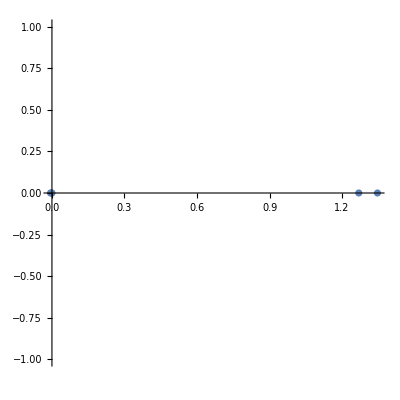

```mathematica
frequency[m1,m2,Rinit,Pinit,S1init,S2init,λf,λi,ϵ]
```

```mathematica
(*
(*data needed to check if the energy is negative*)
ϵ= 3/1000; 
 μ =m1  m2 /(m1+m2); M=m1+m2;
Q1=(1+3 m2/(4 m1));Q2=(1+3 m1/(4 m2));
Linit=Cross[Rinit, Pinit];
SeffLN=(Q1 S1init+ Q2 S2init).Linit;
En=μ ((Pinit.Pinit)/(2 μ^2)-(G M)/Norm[Rinit]) + (2 G ϵ SeffLN)/(Norm[Rinit])^3 //Simplify*)
```